# Lorentz factor c in 1D

-Graphics-

## In 1D

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v=0.9c;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

```mathematica
β[v]
```

0.9

### Lorentz factor

```mathematica
γ[𝓋_]=1/(√(1-β[𝓋]^2));
```

```mathematica
γ[v]
```

2.29416

```mathematica
γPlot1=Plot[γ[𝓋],{𝓋,0,c},FrameLabel->{"v (m/s)","γ"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic,AspectRatio->1];
```

```mathematica
γPlot2=ListPlot[{{v,γ[v]}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

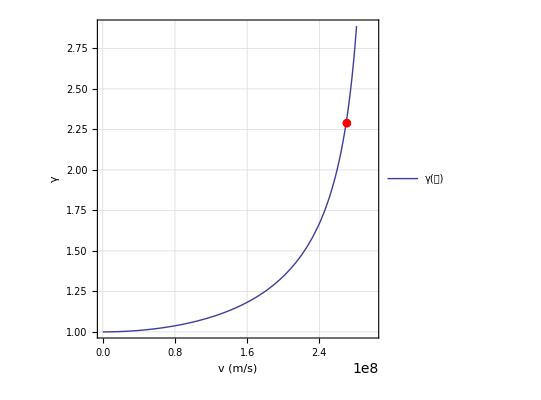

```mathematica
Show[γPlot1,γPlot2]
```

```mathematica
Limit[γ[𝓋],𝓋->c]
```

(-ⅈ) ∞

```mathematica
Limit[γ[𝓋],𝓋->10]//N
```

1.